## RNN Sequence 10 - Rescaled

```mathematica
rescaledSubtractedTS=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\rescaledSubtractedTS.wxf"];
```

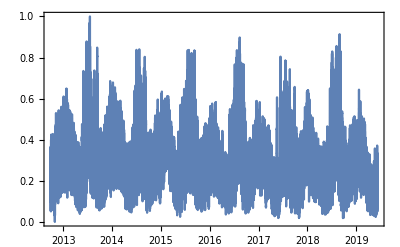

```mathematica
DateListPlot[rescaledSubtractedTS]
```

```mathematica
data=rescaledSubtractedTS//Normal;
```

```mathematica
values=QuantityMagnitude@data[[All,2]];keysp=Partition[values,10,1];valuesp = values[[11;;]];
```

```mathematica
threaddata=Thread[Table[ArrayReshape[keysp[[i]],{1,10}]->valuesp[[i]],{i,1,Length@valuesp}]];
```

```mathematica
Length@data
```

58680

```mathematica
Length@threaddata
```

58670

```mathematica
{trainingdata,testdata}=TakeDrop[threaddata,45000];
```

```mathematica
rnn=NetChain[{GatedRecurrentLayer[32,"Dropout"->{"VariationalInput"->0.3},"Input"->{"Varying",10}],GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.3}],GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.3}],SequenceLastLayer[],LinearLayer[128],Ramp,LinearLayer[1]},"Output"->"Scalar"]
```

NetChain[<>]

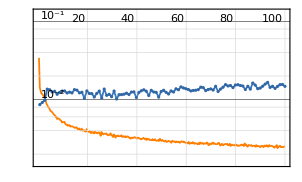
NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
trainednet =  NetTrain[rnn,trainingdata,All,ValidationSet->testdata,BatchSize->800,Method-> "ADAM",MaxTrainingRounds->100]
```

```mathematica
AssociationMap[ PredictorMeasurements[
Predict[trainingdata,Method->#,PerformanceGoal->"DirectTraining"],testdata, "MeanSquare"]&,{"RandomForest"}]
```

<|RandomForest→0.00104951|>

```mathematica
SeedRandom[111];rsample=RandomSample[testdata,2]
```

{{{0.369093,0.37334,0.367965,0.35475,0.343098,0.338917,0.340734,0.358589,0.384605,0.397505}}→0.405578,{{0.132999,0.113477,0.109631,0.112344,0.131025,0.15343,0.209249,0.252979,0.256041,0.250144}}→0.256307}

```mathematica
trainednet[rsample[[2,1]]]
```

NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{{0.132999,0.113477,0.109631,0.112344,0.131025,0.15343,0.209249,0.252979,0.256041,0.250144}}]

```mathematica
sobj=NetStateObject[trainednet]
```

NetStateObject::arg1: First argument to NetStateObject should be a valid net.

$Failed

```mathematica
results=Union@Flatten@NestList[Drop[Join[#,{trainednet[#]}],1]&,testdata[[1,1]],100]
```

{0.169055,108,NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.7min  examples/s:13383
data | ,,  training examples:45000  validation examples:13670  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.49×10^-3
validation | ,,  loss:1.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{{0.254679,0.174088,0.193649,0.171725,0.169055,0.171057,0.173627,0.220757,0.292202,0.31872}}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}
 |  |  |  |

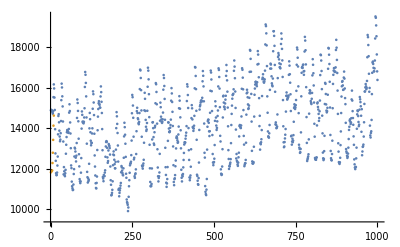

```mathematica
ListPlot[{testdata[[1;;1000,2]],results}]
```